```mathematica
Subscript[x, i] = 0;
Subscript[x, f] = 10;
Subscript[y, i] = 0;
Subscript[y, f] = 10;
Subscript[d, i] = 0;
Subscript[d, f] = 0;
w = 2.125;
```

```mathematica
Plot[c[x], {x, Subscript[x, i], Subscript[x, f]}, PlotRange->{{Subscript[x, i], Subscript[x, f]},{Subscript[y, i], Subscript[y, f]}}]
```

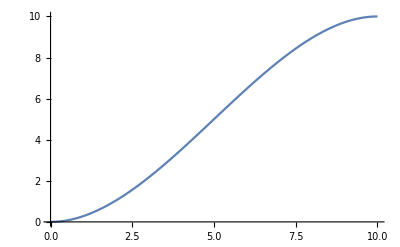

```mathematica
Subscript[h, 1][x_] =2(x^3)-3(x^2)+1 ;(*h00*)
Subscript[h, 2][x_] = x^3 - 2(x^2)+x ; (*h10*)
Subscript[h, 3][x_] = -2(x^3)+3(x^2); (*h01*)
Subscript[h, 4][x_] = x^3-x^2 ; (*h11*)

c[x_] = Subscript[y, i]*Subscript[h, 1][(x-Subscript[x, i])/(Subscript[x, f]-Subscript[x, i])]+ Subscript[d, i]*Subscript[h, 2][(x-Subscript[x, i])/(Subscript[x, f]-Subscript[x, i])]+ Subscript[y, f]*Subscript[h, 3][(x-Subscript[x, i])/(Subscript[x, f]-Subscript[x, i])] + Subscript[d, f]*Subscript[h, 4][(x-Subscript[x, i])/(Subscript[x, f]-Subscript[x, i])];
```

```mathematica
(*Solve[Subscript[x, c]==x-Sin[ArcTan[c'[Subscript[x, c]]]],Subscript[x, c]]*)
```